# Discontinuous Galerkin

## Nodal Formulation in 1 space dimension

by Manuel A. Diaz, NTU, 2012.07.29

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

#### Change Notebook Background

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

#### Set Notebook background back to default

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[0,0,0]]
```

#### Load Notation package and create symbols

```mathematica
Needs["Notation`"]
```

```mathematica
Symbolize[Subscript[u, j-1/2]^+];Symbolize[Subscript[u, j-1/2]^-];Symbolize[Subscript[f̂, j-1/2]];
```

```mathematica
Symbolize[Subscript[u, j+1/2]^-];Symbolize[Subscript[u, j+1/2]^+];Symbolize[Subscript[f̂, j+1/2]];
```

```mathematica
Symbolize[u^+];Symbolize[u^-];
```

## Math Objects

Math Objects that we are going to be dealing with in Nodal DG

### Mass Matrix

Well this one is very simple, if we are using legendre polynomial as our base fucntion, we have done this manny times by now,

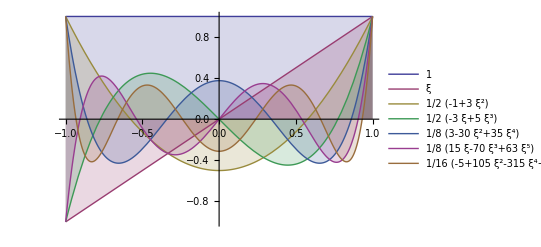

```mathematica
legendreP =Table[LegendreP[i,ξ],{i,0,6}];Table[Subscript[P, i]=legendreP[[i+1]],{i,0,6}];
Plot[Evaluate[legendreP],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

The mass matrix, M, is then defined as

```mathematica
M = Table[∫_-1^1 Subscript[P, i] Subscript[P, j] ⅆξ,{i,0,6},{j,0,6}];M//Simplify//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2/5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2/7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2/9 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2/11 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2/13)

and

```mathematica
invM = Inverse[M];invM//Simplify//MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 5/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 7/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 9/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 11/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 13/2)

### Stiffness Matrix

```mathematica
Clear[x]; dLegendreP[j_,x_]:= D[LegendreP[j,x], x];
```

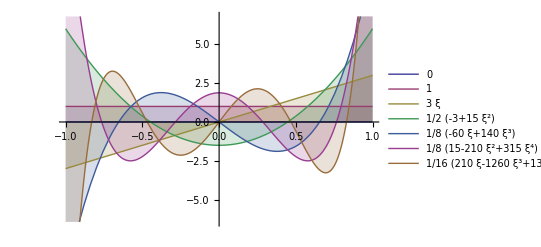

```mathematica
dlegendreP = Table[dLegendreP[i,ξ],{i,0,6}];
Table[Subscript[dP, i]=dLegendreP[i,ξ],{i,0,6}];
Plot[Evaluate[dlegendreP],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
S = Table[∫_-1^1 Subscript[P, i] Subscript[dP, j] ⅆξ,{i,0,6},{j,0,6}];S//Simplify//MatrixForm
```

(0 | 2 | 0 | 2 | 0 | 2 | 0
0 | 0 | 2 | 0 | 2 | 0 | 2
0 | 0 | 0 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Is there any relation between M and S?

Lets explore the case that M = α.S:

```mathematica
Dr = invM.S; Dr //MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 3 | 0 | 3 | 0 | 3
0 | 0 | 0 | 5 | 0 | 5 | 0
0 | 0 | 0 | 0 | 7 | 0 | 7
0 | 0 | 0 | 0 | 0 | 9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 11
0 | 0 | 0 | 0 | 0 | 0 | 0)

An Amazing relation!

### Vandermonde Matrix

In Nodal DG this is our most important interpolation tool and the key to translate nodal information to legendre coeficients and viceversa. The Vandermonde matrix is defined as,

```mathematica
Vandermonde =  Table[LegendreP[n,Subscript[x, i]],{i,1,5},{n,0,4}]; Vandermonde//MatrixForm
```

(1 | x_1 | 1/2 (-1+3 x_1^2) | 1/2 (-3 x_1+5 x_1^3) | 1/8 (3-30 x_1^2+35 x_1^4)
1 | x_2 | 1/2 (-1+3 x_2^2) | 1/2 (-3 x_2+5 x_2^3) | 1/8 (3-30 x_2^2+35 x_2^4)
1 | x_3 | 1/2 (-1+3 x_3^2) | 1/2 (-3 x_3+5 x_3^3) | 1/8 (3-30 x_3^2+35 x_3^4)
1 | x_4 | 1/2 (-1+3 x_4^2) | 1/2 (-3 x_4+5 x_4^3) | 1/8 (3-30 x_4^2+35 x_4^4)
1 | x_5 | 1/2 (-1+3 x_5^2) | 1/2 (-3 x_5+5 x_5^3) | 1/8 (3-30 x_5^2+35 x_5^4))

where x_i are the nodes coordinates inside our element.
The rules of the game goes as follows:

u_coef = inv[V].u_nodes,   and viceversa     u_nodes = [V].u_coef

It is important to realize that in nodal DG we use Lagrange Polynomials to interpolate data at their respectives nodes (like we do in FEM). How good this interpolation is done? well we rely on the interpolated data from the Legrendre Expansion as the core Idea behind the method.

### Relations of the Nodal data and the Modal data (Legendre Coefs)

The first tool that we need is in our toolbox is how derivate a function us expansion on Legendre Coeficients,

Let us define any function F, e.g.:

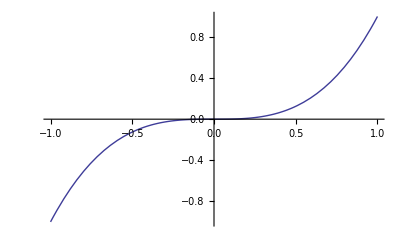

```mathematica
F[x_] := x^3; Plot[F[ξ],{ξ,-1,1}]
```

and it’s derivate,

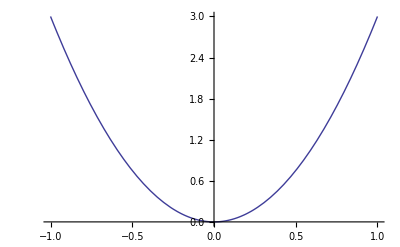

```mathematica
dF[x_] := 3x^2; Plot[dF[ξ],{ξ,-1,1}]
```

Second. We know need a discrete domain to compute this information, let’s use

Chevishev nodes

```mathematica
x = Table[ i,{i,-1,1,1/2}]
```

{-1,-1/2,0,1/2,1}

```mathematica
Table[Subscript[ξ, i] = Sin[1/2 π x[[i]]],{i,1,5}] (* nodes in a standard element *)
```

{-1,-1/(√2),0,1/(√2),1}

```mathematica
Subscript[f, nodes] = Table[F[Subscript[ξ, i]],{i,1,5}]
```

{-1,-1/(2 √2),0,1/(2 √2),1}

```mathematica
Subscript[df, nodes] =Table[dF[Subscript[ξ, i]],{i,1,5}]
```

{3,3/2,0,3/2,3}

Lets translate our nodal information to Legendre coefficients, build our vandermonde Matrix,

```mathematica
V =  Table[LegendreP[n,Subscript[ξ, i]],{i,1,5},{n,0,4}]; V//MatrixForm
```

(1 | -1 | 1 | -1 | 1
1 | -1/(√2) | 1/4 | 1/(4 √2) | -13/32
1 | 0 | -1/2 | 0 | 3/8
1 | 1/(√2) | 1/4 | -1/(4 √2) | -13/32
1 | 1 | 1 | 1 | 1)

and it’s Inverse, invV,

```mathematica
invV = Inverse[V]; invV//MatrixForm
```

(1/30 | 4/15 | 2/5 | 4/15 | 1/30
-1/10 | -(2 √2)/5 | 0 | (2 √2)/5 | 1/10
5/21 | 4/21 | -6/7 | 4/21 | 5/21
-2/5 | (2 √2)/5 | 0 | -(2 √2)/5 | 2/5
8/35 | -16/35 | 16/35 | -16/35 | 8/35)

Then let us compute our Legendre coeficients, f_coef,

```mathematica
Subscript[f, coef]= invV.Subscript[f, nodes]
```

{0,3/5,0,2/5,0}

#### Here we have an intermission to ask ourselves:

Is there any way I can find a parameter α such that,

[V^-1dF/dξ] = α . [V^-1F ]

in words: such that the legendre coeficients of the function derivative can be directly computed with the legendre coeficients of the original Function?

Let’s explore this possibility:

```mathematica
Subscript[df, coef] = invV.Subscript[df, nodes]
```

{1,0,2,0,0}

This last results will be our objetive,

Note the relation between M and S, and let us built this relation for our model problem

```mathematica
Dr = DiagonalMatrix[{1,3,5,7,9,11},1,5]+DiagonalMatrix[{1,3,5,7,9,11},3,5]+
DiagonalMatrix[{1,3,5,7,9,11},5,5]; Dr //MatrixForm
```

(0 | 1 | 0 | 1 | 0
0 | 0 | 3 | 0 | 3
0 | 0 | 0 | 5 | 0
0 | 0 | 0 | 0 | 7
0 | 0 | 0 | 0 | 0)

now if make the comparison of results,

```mathematica
Subscript[df, coef]==Dr.Subscript[f, coef]
```

True

Wow!! we have found a nice feature that can save a lot of numerical work!

### Mass Matrix for Nodal DG

For this part let us compare our computation with the examples in the text: Nodal DG 2008.
Let us use now LGL points.

#### Legendre-Gauss-Lobatto (LGL) Polynomials

```mathematica
lobatto = Table[Subscript[P, k]-Subscript[P, k-2],{k,2,5}] //Simplify;
```

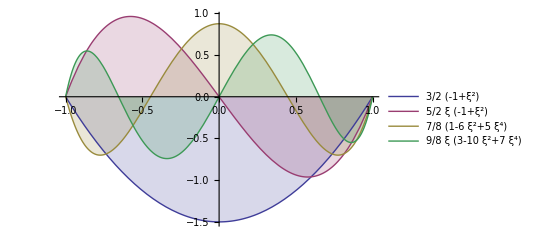

```mathematica
Plot[Evaluate[lobatto],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[Lo, i]= lobatto[[i]],{i,1,4}]//TableForm
```

3/2 (-1+ξ^2)
5/2 ξ (-1+ξ^2)
7/8 (1-6 ξ^2+5 ξ^4)
9/8 ξ (3-10 ξ^2+7 ξ^4)

Lobatto roots and weights

```mathematica
abscissas = -Sort[List @@ Roots[Subscript[Lo, 4]==0,ξ][[All,2]],Greater];
Table[Subscript[ξ, i]=abscissas[[i]],{i,1,5}]
```

{-1,-√(3/7),0,√(3/7),1}

```mathematica
V =  Table[LegendreP[n,Subscript[ξ, i]],{i,1,5},{n,0,4}]; V//MatrixForm
```

(1 | -1 | 1 | -1 | 1
1 | -√(3/7) | 1/7 | (3 √(3/7))/7 | -3/7
1 | 0 | -1/2 | 0 | 3/8
1 | √(3/7) | 1/7 | -(3 √(3/7))/7 | -3/7
1 | 1 | 1 | 1 | 1)

```mathematica
Subscript[M, nodal]=Inverse[V.Transpose[V]]; Subscript[M, nodal]//N//MatrixForm
```

(0.25 | -0.138038 | -0.0977778 | 0.0758157 | -0.04
-0.138038 | 0.901358 | -0.324938 | -0.241975 | 0.0758157
-0.0977778 | -0.324938 | 1.20099 | -0.324938 | -0.0977778
0.0758157 | -0.241975 | -0.324938 | 0.901358 | -0.138038
-0.04 | 0.0758157 | -0.0977778 | -0.138038 | 0.25)

Becuase we are using lagrange Polynomials as our base function is no surprice that the Mass matrix is a full matrix.

### Grad Vandermonde

Similarly to the Vandermonde Matrix,

```mathematica
Vr =  Table[dLegendreP[n,y]/.y->Subscript[ξ, i],{i,1,5},{n,0,4}];Vr//MatrixForm
```

(0 | 1 | -3 | 6 | -10
0 | 1 | -3 √(3/7) | 12/7 | 0
0 | 1 | 0 | -3/2 | 0
0 | 1 | 3 √(3/7) | 12/7 | 0
0 | 1 | 3 | 6 | 10)

### Dr Matrix for Nodal DG

```mathematica
Dr = Vr.Inverse[V]; Dr//N//MatrixForm
```

(-5. | 6.7565 | -2.66667 | 1.41016 | -0.5
-1.24099 | 0. | 1.74574 | -0.763763 | 0.25901
0.375 | -1.33658 | 0. | 1.33658 | -0.375
-0.25901 | 0.763763 | -1.74574 | 0. | 1.24099
0.5 | -1.41016 | 2.66667 | -6.7565 | 5.)

We are in perfect agreement with the Dr. Hestaven and Dr. Warburton ; )

Note that this matrix is Skew-antisymmetric.

## Mesh 1D

Define Domain x ∈ [ a , b ],
We then divide it into ‘n’ small cells/elements

```mathematica
a= 0; b = 1; n = 10; nf = n+1; Δx = (b-a)/n;
```

```mathematica
Table [Subscript[x, i-1/2]=a+ i Δx,{i,0,n}]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

Define Intervals I_j:

```mathematica
Table[Subscript[I, j]={Subscript[x, j-3/2],Subscript[x, j-1/2]},{j,1,n}]
```

{{0,1/10},{1/10,1/5},{1/5,3/10},{3/10,2/5},{2/5,1/2},{1/2,3/5},{3/5,7/10},{7/10,4/5},{4/5,9/10},{9/10,1}}

Define element sizes h_j:

```mathematica
Table[Subscript[h, j]=(Subscript[x, j-1/2]-Subscript[x, j-3/2]),{j,1,n}]
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}

Define element centers x_j :

```mathematica
Table[Subscript[x, j]=(Subscript[x, j-3/2]+Subscript[x, j-1/2])/2,{j,1,n}]
```

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

Standar Element Definition I_ξ:

```mathematica
Subscript[I, ξ] = ({{-1, 1}})
```

{{-1,1}}

Therefore the Jacobian metric between this two elements is given by,

```mathematica
J = Subscript[h, j]/2;
```

Now, let us define solution points, ξ_k, inside the standar element:
Lets define a polynomial of degree K=3 on either Legendre / Lobatto points,

```mathematica
K=3;
```

#### Legendre Polynomials

Generating up to 4th degree Legendre Polynomials.

```mathematica
legendreP = Table[LegendreP[i,x],{i,0,5}];
```

```mathematica
Table[Subscript[p, i]= legendreP[[i+1]],{i,0,5}];
{Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5]}
```

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5)}

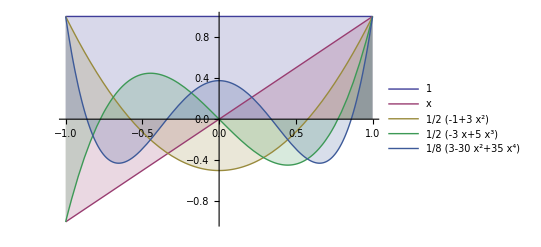

```mathematica
Plot[Evaluate[Most[legendreP]],{x,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

Legendre Roots and weights

```mathematica
abscissas = -Sort[List @@ Roots[Subscript[p, 4]==0,x][[All,2]],Greater]
```

{-√(1/35 (15+2 √30)),-√(1/35 (15-2 √30)),√(1/35 (15-2 √30)),√(1/35 (15+2 √30))}

```mathematica
weights={1/36 (18-√30),1/36 (18+√30),1/36 (18+√30),1/36 (18-√30)};
```

#### Legendre-Gauss-Lobatto (LGL) Polynomials

```mathematica
lobatto = Table[Subscript[p, k]-Subscript[p, k-2],{k,2,5}] //Simplify;
```

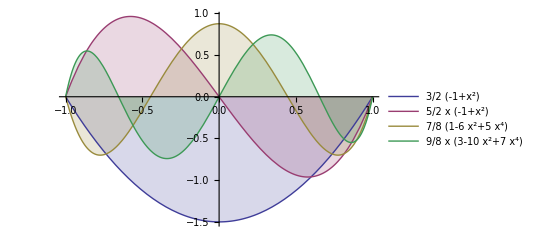

```mathematica
Plot[Evaluate[lobatto],{x,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[Lo, i]= lobatto[[i]],{i,1,4}]//TableForm
```

3/2 (-1+x^2)
5/2 x (-1+x^2)
7/8 (1-6 x^2+5 x^4)
9/8 x (3-10 x^2+7 x^4)

Lobatto roots and weights

```mathematica
abscissas = -Sort[List @@ Roots[Subscript[Lo, 3]==0,x][[All,2]],Greater]
```

{-1,-1/(√5),1/(√5),1}

```mathematica
weights={1/6,5/6,5/6,1/6}
```

{1/6,5/6,5/6,1/6}

Define Subpolynomial Domains over our original Domain. We  define the following mapping for x and ξ (solution points here) :

```mathematica
Subscript[x, 𝒟]=Table[Subscript[x, j]+ J ×abscissas,{j,1,n}];
Subscript[x, 𝒟]//TableForm//N
```

0. | 0.0276393 | 0.0723607 | 0.1
0.1 | 0.127639 | 0.172361 | 0.2
0.2 | 0.227639 | 0.272361 | 0.3
0.3 | 0.327639 | 0.372361 | 0.4
0.4 | 0.427639 | 0.472361 | 0.5
0.5 | 0.527639 | 0.572361 | 0.6
0.6 | 0.627639 | 0.672361 | 0.7
0.7 | 0.727639 | 0.772361 | 0.8
0.8 | 0.827639 | 0.872361 | 0.9
0.9 | 0.927639 | 0.972361 | 1.

Define ' u_(j,k)’ values for every node in our domain.
I will assume an IC as: u(x) = 0.5 +sin(2πx), therefore

```mathematica
Table[Subscript[x, j,k]= Subscript[x, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

```mathematica
u0[x_]:=Sin[2 π x]; (* or *)
(*u0[x_]:= Piecewise[{{2,x<=0.45},{1,x>0.45}}];*)
Subscript[u, 𝒟] = Table[u0[Subscript[x, j,k]],{j,1,10},{k,1,4}];
Subscript[u, 𝒟]//N//TableForm
```

0. | 0.172791 | 0.439153 | 0.587785
0.587785 | 0.718735 | 0.883356 | 0.951057
0.951057 | 0.990147 | 0.990147 | 0.951057
0.951057 | 0.883356 | 0.718735 | 0.587785
0.587785 | 0.439153 | 0.172791 | 0.
0. | -0.172791 | -0.439153 | -0.587785
-0.587785 | -0.718735 | -0.883356 | -0.951057
-0.951057 | -0.990147 | -0.990147 | -0.951057
-0.951057 | -0.883356 | -0.718735 | -0.587785
-0.587785 | -0.439153 | -0.172791 | 0.

Load u_0 into our domain

```mathematica
Table[Subscript[u, j,k]= Subscript[u, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

take for example j=4 and k=1, we should get

```mathematica
Subscript[u, 4,1]
```

√(5/8+(√5)/8)

#### Continuous Case

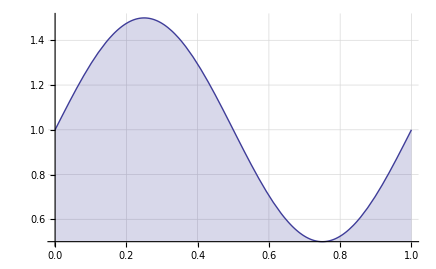

```mathematica
u[x_,t_]:= 0.5(2+Sin[2π x]);
sin =Plot[u[x,t],{x,0,1},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],Filling->Axis]
```

#### Discontinuous Case

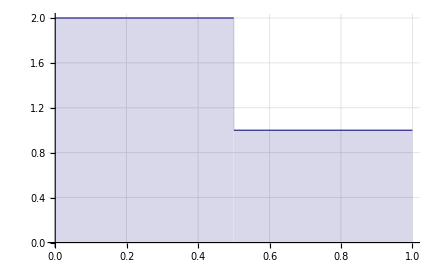

```mathematica
u[x_,t_]:= Piecewise[{{2,x<0.5},{1,x>=0.5}}]
Plot[u[x,t],{x,0,1},PlotRange->{0,2},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],Filling->Axis]
```

Assume t = 0. Evaluate u[x, t] at discrete value points,

## Base function in 1D

Using a Lagrange Base function,

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]}= abscissas;
```

from FEM we have the base functions are defined by the relation [M] {Ne(x)} = {P(x)}, where

```mathematica
P[x_]:= ({{1}, {x}, {x^2}, {x^3}}) (* Monomial Basis *)
```

if we define M as,

```mathematica
M = Table[Subscript[ξ, j]^i,{j,1,4},{i,0,3}]; M//MatrixForm
```

(1 | -1 | 1 | -1
1 | -1/(√5) | 1/5 | -1/(5 √5)
1 | 1/(√5) | 1/5 | 1/(5 √5)
1 | 1 | 1 | 1)

I always performed this:

```mathematica
Ne[x_]:= Transpose[Inverse[M]].P[x]
```

so that my shape functions (lagrange polynomials) are,

```mathematica
Ne[ξ]//Expand
```

{{-1/8+ξ/8+(5 ξ^2)/8-(5 ξ^3)/8},{5/8-(5 √5 ξ)/8-(5 ξ^2)/8+(5 √5 ξ^3)/8},{5/8+(5 √5 ξ)/8-(5 ξ^2)/8-(5 √5 ξ^3)/8},{-1/8-ξ/8+(5 ξ^2)/8+(5 ξ^3)/8}}

As expected this polynomials exhibit a δ_ij property,

```mathematica
Table[Ne[Subscript[ξ, i]],{i,4}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

### Compute u values at I_j faces

If the solutions points ξ_k include points the at the boundaries for the standar element, we can just simply do: (u_(j-1/2))^+ = u_(j,1) and (u_(j+1/2))^- = u_(j,k+1)

```mathematica
SuperPlus[Subscript[u, j-1/2]] = Subscript[u, 𝒟][[All,1]]//N;
SuperPlus[Subscript[u, j-1/2]] //TableForm
```

0.
0.587785
0.951057
0.951057
0.587785
0.
-0.587785
-0.951057
-0.951057
-0.587785

```mathematica
SuperMinus[Subscript[u, j+1/2]] = Subscript[u, 𝒟][[All,4]]//N;
SuperMinus[Subscript[u, j+1/2]] // TableForm
```

0.587785
0.951057
0.951057
0.587785
0.
-0.587785
-0.951057
-0.951057
-0.587785
0.

```mathematica
{SuperPlus[Subscript[u, j-1/2]],SuperMinus[Subscript[u, j+1/2]]}//TableForm
```

0. | 0.587785 | 0.951057 | 0.951057 | 0.587785 | 0. | -0.587785 | -0.951057 | -0.951057 | -0.587785
0.587785 | 0.951057 | 0.951057 | 0.587785 | 0. | -0.587785 | -0.951057 | -0.951057 | -0.587785 | 0.

### Set BC across faces of the domain

Let us set a periodic BC:

```mathematica
SuperPlus[u]=Join[SuperPlus[Subscript[u, j-1/2]],{0}];
SuperMinus[u]=Join[{0},SuperMinus[Subscript[u, j+1/2]]];
```

```mathematica
SuperPlus[u][[nf]]=SuperPlus[u][[1]]; (*right BC*)
SuperMinus[u][[1]]=SuperMinus[u][[nf]]; (*left BC*)
```

Set::setps: u^+ in the part assignment is not a symbol.

Set::setps: u^- in the part assignment is not a symbol.

```mathematica
{SuperPlus[u],SuperMinus[u]}//TableForm
```

0. | 0.587785 | 0.951057 | 0.951057 | 0.587785 | 0. | -0.587785 | -0.951057 | -0.951057 | -0.587785 | 0
0 | 0.587785 | 0.951057 | 0.951057 | 0.587785 | 0. | -0.587785 | -0.951057 | -0.951057 | -0.587785 | 0.

### Numerical Flux

#### Lax Friedrichs

Let’s use in this example the Lax-Friedrichs as our Riemann flux,

```mathematica
(* In this example: Burgers' flux functions *)  
f[u_]:= u^2/2; df [u_]:=u;
```

```mathematica
(* In this example: Linear' flux functions *)  
f[u_]:= u; df [u_]:=1;
```

```mathematica
α= Max[Subscript[u, 𝒟]//N];
```

```mathematica
LF[a_,b_]:= 1/2(f[a]+f[b]-α(b-a))
```

```mathematica
f̂=LF[SuperMinus[u],SuperPlus[u]]; 
f̂//N//TableForm
```

0.
0.587785
0.951057
0.951057
0.587785
0.
-0.587785
-0.951057
-0.951057
-0.587785
0.

```mathematica
SuperPlus[Subscript[f̂, j-1/2]]=Most[f̂]
```

{0.,0.587785,0.951057,0.951057,0.587785,0.,-0.587785,-0.951057,-0.951057,-0.587785}

```mathematica
SuperMinus[Subscript[f̂, j+1/2]]=Rest[f̂]
```

{0.587785,0.951057,0.951057,0.587785,0.,-0.587785,-0.951057,-0.951057,-0.587785,0.}

#### Upwind

```mathematica
c = 1; f[u_]:= c u; df [u_]:=c;
```

```mathematica
Upwind[a_,b_]:= (c a+c b)/2+(c a-c b)/2;
```

```mathematica
Upwind[1,1]
```

1

```mathematica
f̂=Upwind[SuperPlus[u],SuperMinus[u]];
f̂//N//TableForm
```

0.
0.587785
0.951057
0.951057
0.587785
0.
-0.587785
-0.951057
-0.951057
-0.587785
0.

This is like taking the left values of at every element boundary

```mathematica
SuperPlus[u]
```

{0.,0.587785,0.951057,0.951057,0.587785,0.,-0.587785,-0.951057,-0.951057,-0.587785,0}

```mathematica
SuperPlus[Subscript[f̂, j-1/2]]=Most[f̂] (* Left *)
```

{0.,0.587785,0.951057,0.951057,0.587785,0.,-0.587785,-0.951057,-0.951057,-0.587785}

```mathematica
SuperMinus[Subscript[f̂, j+1/2]]=Rest[f̂] (* Rigth *)
```

{0.587785,0.951057,0.951057,0.587785,0.,-0.587785,-0.951057,-0.951057,-0.587785,0.}

### Vandermonde Matrix

```mathematica
V =  Table[LegendreP[j-1,Subscript[ξ, i]],{i,1,4},{j,1,4}]; V//MatrixForm
```

(1 | -1 | 1 | -1
1 | -1/(√5) | -1/5 | 1/(√5)
1 | 1/(√5) | -1/5 | -1/(√5)
1 | 1 | 1 | 1)

therefore the inverser of our mass matrix is:

```mathematica
normalizedLegendre = Orthogonalize[{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},Integrate[#1 #2,{x,-1,1}]&] //Expand;
```

```mathematica
Vnormal =  Table[normalizedLegendre[[j]]/.x->Subscript[ξ, i],{i,1,4},{j,1,4}]; Vnormal//N//MatrixForm
```

(0.707107 | -1.22474 | 1.58114 | -1.87083
0.707107 | -0.547723 | -0.316228 | 0.83666
0.707107 | 0.547723 | -0.316228 | -0.83666
0.707107 | 1.22474 | 1.58114 | 1.87083)

```mathematica
invM = Vnormal.Transpose[Vnormal]//N; invM//MatrixForm
```

(8. | -0.894427 | 0.894427 | -2.
-0.894427 | 1.6 | -0.4 | 0.894427
0.894427 | -0.4 | 1.6 | -0.894427
-2. | 0.894427 | -0.894427 | 8.)

### Lift Operator

Our last remaining operator of the day.
Lets take advantage of the previous computations to compute the following expresion,
∫_-1^1 (c u_h-c u^*)Ne[ξ]ⅆξ = (c u_h-c u^*)|_(ξ_K+1)Ne[1] - (c u_h-c u^*)|_ξ_1 Ne[-1]

```mathematica
Ne[-1]//MatrixForm
```

(1
0
0
0)

```mathematica
Ne[1]//MatrixForm
```

(0
0
0
1)

```mathematica
LIFT = invM.Transpose[{Ne[-1],Ne[1]}]; LIFT //MatrixForm
```

((8.) | (-2.)
(-0.894427) | (0.894427)
(0.894427) | (-0.894427)
(-2.) | (8.))

```mathematica
fl = {c SuperPlus[Subscript[u, j-1/2]] -SuperPlus[Subscript[f̂, j-1/2]]}
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
fr = {c SuperMinus[Subscript[u, j+1/2]] -SuperMinus[Subscript[f̂, j+1/2]]}
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
du = Transpose[{{fl},{fr}}]; du//MatrixForm
```

((0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.))

therefore we compute the surface term by doing

```mathematica
surfaceTerm = LIFT.du ;
```